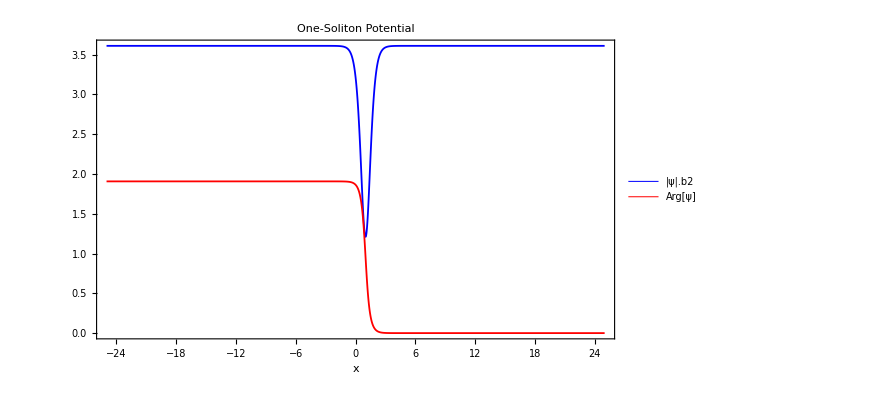

```mathematica
(* ::Title::*)(*Numerical DST for the Single-Soliton Potential*)(*The SolitonDST library must be loaded before this block.*)(* ::Section::*)(*1. Simulation Parameters*)

ClearAll[precision,domainWidth,backgroundAmplitude,discretizationDegree,numPoints,stepSize,integrationSteps,solitonEigenvalue,solitonPosition,time,nu,x,z,oneSolitonPotential,normingConstantRho,spatialGrid,potentialData,phaseMinus,phasePlus,potentialPlot,singleSolitonA,singleSolitonRealA,numericalEigenvalue,numericalRho,solitonResult,zetaPlotMin,zetaPlotMax,numSpectralPoints,zetaPlotGrid,spectralPlotValues,spectralRealData,spectralImaginaryData,spectralCoefficientPlot];

precision=100;

domainWidth=N[50,precision];

backgroundAmplitude=N[1.9,precision];

discretizationDegree=11;

numPoints=2^discretizationDegree;

stepSize=domainWidth/numPoints;

integrationSteps=ConstantArray[stepSize,numPoints];


(*Soliton parameters*)

solitonEigenvalue=N[-1.1,precision];

solitonPosition=N[1.0,precision];

nu=Sqrt[backgroundAmplitude^2-solitonEigenvalue^2];

(* ::Section::*)
(*2. Single-Soliton Potential*)

Clear[oneSolitonPotential,normingConstantRho];

oneSolitonPotential[x_?NumericQ]:=(1/backgroundAmplitude)*(solitonEigenvalue-I nu)*(solitonEigenvalue +I nu Tanh[nu (x-solitonPosition)]);

normingConstantRho[t_?NumericQ]:=-2/backgroundAmplitude I nu^2 Exp[2 nu solitonPosition];

(* ::Section::*)
(*3. Spatial Grid,Potential,and Boundary Phases*)

spatialGrid=Table[-domainWidth/2+stepSize (i-1/2),{i,1,numPoints}];

potentialData=oneSolitonPotential/@spatialGrid;

phaseMinus=Arg[First[potentialData]];

phasePlus=Arg[Last[potentialData]];


(* ::Section::*)
(*4. Potential Visualization*)

potentialPlot=ListLinePlot[{Transpose[{spatialGrid,Abs[potentialData]^2}],Transpose[{spatialGrid,Arg[potentialData]}]},Frame->True,Axes->False,FrameLabel->{"x",""},PlotLegends->{"|ψ|.b2","Arg[ψ]"},PlotStyle->{Directive[Blue,Thickness[0.002]],Directive[Red,Thickness[0.002]]},PlotLabel->Style["One-Soliton Potential",14,Bold],PlotRange->All,ImageSize->650];

Print[potentialPlot];
```

```mathematica
(* ::Section::*)
(*5. Eigenvalue Refinement*)

Clear[singleSolitonA,singleSolitonRealA];

singleSolitonA[z_?NumericQ]:=SolitonDST`aDS[z,backgroundAmplitude,precision,potentialData,integrationSteps,numPoints,domainWidth,phaseMinus,phasePlus];

singleSolitonRealA[z_?NumericQ]:=Re[singleSolitonA[z]];

numericalEigenvalue=Module[{z},z/.FindRoot[singleSolitonRealA[z]==0,{z,solitonEigenvalue},WorkingPrecision->precision]];

numericalEigenvalue - solitonEigenvalue
(* ::Section::*)
(*6. Norming Constant*)

numericalRho=SolitonDST`RhoDS[numericalEigenvalue,backgroundAmplitude,precision,potentialData,integrationSteps,numPoints,domainWidth,phaseMinus,phasePlus];


(* ::Section::*)
(*7. Results*)

Grid[{{"Discretization degree","Spatial interval","Prescribed eigenvalue","Refined eigenvalue","ρ"},{discretizationDegree,NumberForm[#,8]&/@{-domainWidth/2,domainWidth/2},NumberForm[solitonEigenvalue,12],NumberForm[numericalEigenvalue,12],NumberForm[numericalRho,12]}},Frame->All,Alignment->Center,Background->{None,{LightGray,None}},Spacings->{2,1},ItemStyle->Directive[FontSize->12]]
```

0.

Discretization degree | Spatial interval | Prescribed eigenvalue | Refined eigenvalue | ρ
11 | {-25.000000,25.000000} | -1.1 | -1.10000000000 | -8.52126841751×10^-15-55.9930836449 ⅈ